```mathematica
Function[x,(3.7262912531793 x (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))/((5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))]
```

Function[x,(3.72629 x (-0.495117+36.4408 x^2-474.677 x^4+x^6))/((5.16692-112.205 x^2+1. x^4) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))]

```mathematica
%84[1.1]
```

9.2462

```mathematica
%84[1.15]
```

10.6102

```mathematica
%84[0.532]
```

0.907118

```mathematica
%84[0.5]
```

0.733666

```mathematica
%84[1]
```

6.87847

```mathematica
Function[x,(-0.13340934590809223+46.19782759947689 x^2-9319.960034168205 x^4+820875.2357290179 x^6-3.454499271858802*^7 x^8+7.554807891116797*^8 x^10-8.388540231321073*^9 x^12+3.763097199843844*^10 x^14-5.375117248494613*^8 x^16+2.8982736048942916*^6 x^18-9377.774385177327 x^20+11.178873759537902 x^22)/((5.166916072738272-112.20528246809232 x^2+1. x^4)^2 (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6) (-0.02826589756799342+6.952323756786463 x^2-132.89854692493893 x^4+1. x^6) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))]
```

Function[x,(-0.133409+46.1978 x^2-9319.96 x^4+820875. x^6-3.4545×10^7 x^8+7.55481×10^8 x^10-8.38854×10^9 x^12+3.7631×10^10 x^14-5.37512×10^8 x^16+2.89827×10^6 x^18-9377.77 x^20+11.1789 x^22)/((5.16692-112.205 x^2+1. x^4)^2 (-0.495117+36.4408 x^2-474.677 x^4+x^6) (-0.0282659+6.95232 x^2-132.899 x^4+1. x^6) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))]

```mathematica
%86[1.1]
```

26.0392

```mathematica
%86[0.5]
```

5.07003

```mathematica
%86[1]
```

21.3944

```mathematica
Function[0.38+0.62*BesselJ[0,5.52/x]]
```

0.38+0.62 BesselJ[0,5.52/x]&

```mathematica
,1.7
```

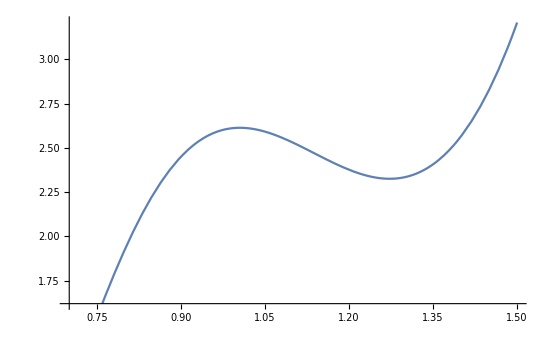

```mathematica
Plot[(0.38+0.62 BesselJ[0,5.52/x])*((3.7262912531793 x (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))/((5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))),{x,0.7,1.5}]
```

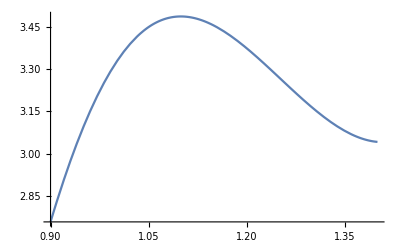

```mathematica
Plot[(0.377+0.623 BesselJ[0,(5.52*1.1)/x])*((3.7262912531793 x (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))/((5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))),{x,0.9,1.4}]
```

```mathematica
Simplify[(3.7262912531793 x (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))/((5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))*E^(-a/x)]
```

(3.72629 ⅇ^(-a/x) x (-0.495117+36.4408 x^2-474.677 x^4+x^6))/((5.16692-112.205 x^2+1. x^4) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))

```mathematica
data={{0.4,0.25},{0.532,1.3},{0.7,2.6}}
FindFit[data,(3.7262912531793 ⅇ^(-a/x) x (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))/((5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))),a,x]
```

{{0.4,0.25},{0.532,1.3},{0.7,2.6}}

{a→-0.116848}

```mathematica
(3.7262912531793 ⅇ^(0.116847820014274/x) x (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))/((5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))
```

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
Simplify[(3.7262912531793 ⅇ^(0.116847820014274/x) x (-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6))/((5.166916072738272-112.20528246809232 x^2+1. x^4) √(1+(85.3388526237744 x^2-1853.2273273560002 x^4+16.5164 x^6)/(-0.49511676816+36.4408312296 x^2-474.67678 x^4+x^6)))]
```

(3.72629 ⅇ^(0.116848/x) x (-0.495117+36.4408 x^2-474.677 x^4+x^6))/((5.16692-112.205 x^2+1. x^4) √(1+(85.3389 x^2-1853.23 x^4+16.5164 x^6)/(-0.495117+36.4408 x^2-474.677 x^4+x^6)))

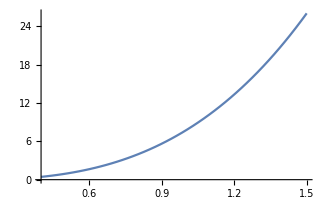

```mathematica
Plot[%141,{x,0.4,1.5}]
```

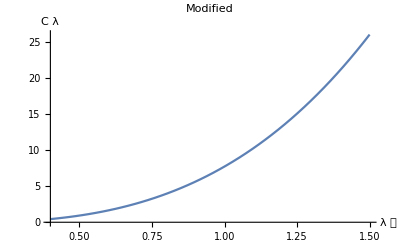

```mathematica
Show[%144,AxesLabel->{HoldForm[λ ㎛],HoldForm[C λ]},PlotLabel->HoldForm[Modified],LabelStyle->{GrayLevel[0],Bold,Italic}]
```

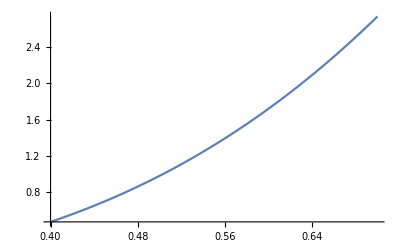

```mathematica
Plot[%136,{x,0.4,0.7}]
```

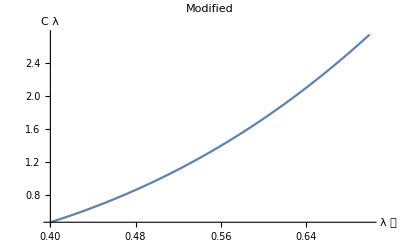

```mathematica
Show[%138,AxesLabel->{HoldForm[λ ㎛],HoldForm[C λ]},PlotLabel->HoldForm[Modified],LabelStyle->{GrayLevel[0],Bold,Italic}]
```

```mathematica
Show[%138,AxesLabel->{HoldForm[λ ㎛],HoldForm[C λ]},PlotLabel->HoldForm[Modified],LabelStyle->{GrayLevel[0],Bold,Italic}]
```

-Graphics-

```mathematica
λ ㎛
```